## Step-Wise Polymerization

Outline:

We have a (brute-force) function which reptates N m-monomer polymer chains w/o collisions

We’ll start with many non-colliding dimers and allow them to reptate

This is not super fast in the beginning.
Here’s a breakdown of the timing. Ideally we’d use temporal coherence using InsertionSort or similar

Number of Dimers  85

Bounding Box Collisions  0

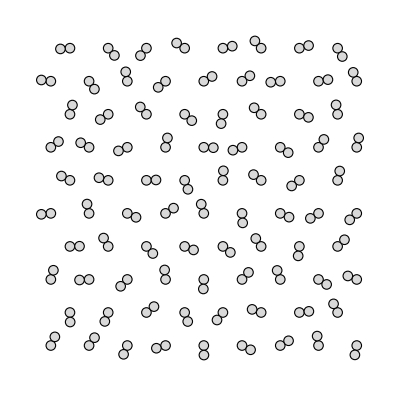

```mathematica
SeedRandom[1111];
listOfPositions=hexagonalDimerConfiguration[35];
Echo[Length[listOfPositions],"Number of Dimers"];
bbs=axesAlignedBoundingBoxes/@listOfPositions;
Echo[connectivityMatrix[bbs]["ExplicitLength"],"Bounding Box Collisions"];
graphicMultiple=Graphics[chainGraphic/@listOfPositions]
```

```mathematica
Block[{
viscousDragging,
singleCollisionDetections,
multipleCollisionsDetection},

viscousDragging=First[RepeatedTiming[displacements[RandomInteger[Range[Length[#]]],#,.05,.1,RandomReal[2π]]&/@listOfPositions]];
singleCollisionDetections=First[RepeatedTiming[moveSingleChain[#,.05]&/@listOfPositions]];
multipleCollisionsDetection=QuietEcho[First[RepeatedTiming[moveAllChains[listOfPositions,.1]]]];

Echo[viscousDragging,"Viscous Dragging Time:"];
Echo[singleCollisionDetections,"Single Collision Detection Time:"];
Echo[multipleCollisionsDetection,"Multiple Collisions Detection Time:"];

]
```

Viscous Dragging Time:  0.00361059

Single Collision Detection Time:  0.00639035

Multiple Collisions Detection Time:  0.0148309

We keep track of the end particles

If any two collide, we merge the chains

we won’t concern ourselves with loops for now

Notes:

The reptation code makes use of `Nearest`, which is considerably slower for periodic boundary distances

We’ll deal with this later (?)

## Simulation

Dynamic

```mathematica
Dynamic[Graphics[chainGraphic/@listOfPositions]]
```

```mathematica
QuietEcho[
Do[
listOfPositions=moveAllChains[listOfPositions,.05],
{5000}]
]
```

Frames

```mathematica
nestListWithMonitor[f_,init_,n_]:=Module[{it=0},
PrintTemporary[ProgressIndicator[Dynamic[it/n]]];
NestList[(it++;f[#])&,init,n]]
```

```mathematica
SeedRandom[1111];
positions=QuietEcho[nestListWithMonitor[moveAllChains[#,0.05]&,listOfPositions,40000]];
```

```mathematica
Length[cleanPositions=DeleteDuplicates[positions]]
```

36332

```mathematica
Export["step-growth-polymerization_85-dimers.mx",cleanPositions]
```

step-growth-polymerization_85-dimers.mx

```mathematica
numberChains=Length/@cleanPositions;
mergers=Extract[cleanPositions,List/@Most[Accumulate[Prepend[Length/@Split[numberChains],1]]]];
mergerFrames=Table[Graphics[chainGraphic/@mergers[[i]],ImageSize->200],{i,Length[mergers]}];
Multicolumn[mergerFrames,5,Appearance->"Horizontal",Frame->All]
```

## Initialization Functions

### Visualization

```mathematica
chainGraphic[positions_,bb_,col_:RandomColor[]]:= {
{Opacity[0.25],col,Rectangle@@Transpose[bb]},
{FaceForm[None],EdgeForm[col//Darker],Disk[#,1/2]&/@positions[[2;;-2]]},
{FaceForm[col//Darker],EdgeForm[Black],Disk[#,1/2]&/@positions[[{1,-1}]]}
}

chainGraphic[positions_]:= {
{Circle[#,1/2]&/@positions[[2;;-2]]},
{FaceForm[LightGray],EdgeForm[Black],Disk[#,1/2]&/@positions[[{1,-1}]]}
}

chainGraphic[positions_?polymerLoopQ]:={Circle[#,1/2]&/@positions}
```

### Correlated Polymers

```mathematica
collisionQ[nf_NearestFunction,bondLength_:1][candidatePt_]:=First[nf[candidatePt]]<bondLength

angularRange[correlation_]:={-1,1}(1-correlation)π

addCorrelatedParticleToChain[correlation_][chainSoFar_]:=Block[{
nf=Nearest[chainSoFar->"Distance"],
angleRange=angularRange[correlation],
lastAngle=ArcTan@@(chainSoFar[[-1]]-chainSoFar[[-2]]),
newAngle,candidate,collision
},

newAngle=RandomReal[angleRange]+lastAngle;
candidate=Last[chainSoFar]+AngleVector[newAngle];

collision=collisionQ[nf][candidate];
If[collision,chainSoFar,Append[chainSoFar,candidate]]

]

Clear[collisionFreeCorrelatedPolymerChain2D]
collisionFreeCorrelatedPolymerChain2D[numberUnits_,correlation_,origin_:{0,0},maxAttempts_:100]:=With[{start=Join[{origin},{AngleVector[origin,RandomReal[angularRange[correlation]]]}]},
NestWhile[addCorrelatedParticleToChain[correlation],start,Length[#]<numberUnits&,1,maxAttempts]
]

randomDimer[origin_]:=Join[{origin},{AngleVector[origin,RandomReal[2π]]}]
testDimerConfiguration[numberDimers_,size_]:=Table[randomDimer[RandomReal[{-size/2,size/2},2]],numberDimers]
initialDimerConfiguration[numberDimers_,size_]:=Block[{dimers=testDimerConfiguration[numberDimers,size],bbs,collisions},
bbs=axesAlignedBoundingBoxes/@dimers;
collisions=connectivityMatrix[bbs]["ExplicitLength"];
If[collisions>0,initialDimerConfiguration[numberDimers,size],dimers]
]

hexagonalDimerConfiguration[size_]:=Block[{hexagonalLatticeVectors={{1,0},{1/2,Sqrt[3]/2}},latticeCoords=Tuples[Range[-size,size,4],2],pts,dimers,bbs,collisions},
pts=Select[latticeCoords.hexagonalLatticeVectors,size/2>#[[1]]>-size/2&&size/2>#[[2]]>-size/2&];
randomDimer/@(pts+RandomReal[{-0.001,0.001},Dimensions[pts]])
]
```

### Viscous Dragging

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]
```

```mathematica
displacementsBase[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
newPositions[index_] := newPositions[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex]},
newPositions[nextIndex] + Δ[[index]]
];
newPositions/@Range[Length[Δ]]
]

Clear[displacements]
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
displacementsBase[perturbedIndex,positionList,s,ν,θ]

displacements[perturbedIndex_,positionList_?polymerLoopQ,s_,ν_,θ_]:=Block[{firstStep,angle,disp,squaredNorm,minimumS,newPositions},

firstStep=displacementsBase[perturbedIndex,positionList,s,ν,θ];
(*If[polymerLoopQ[firstStep],Return[firstStep]];*)
angle=ArcTan@@(firstStep[[1]]-firstStep[[-1]]);

newPositions=displacementsBase[Length[positionList],firstStep,ds,ν,angle];
disp=Subtract@@newPositions[[{1,-1}]];
squaredNorm=disp.disp;

enforceClosedLoopEnd[newPositions/.First[Quiet[FindRoot[squaredNorm,{ds,s,0.,1.},AccuracyGoal->4,PrecisionGoal->4]]]]

]
```

```mathematica
polymerLoopQ[particles_]:=Norm[particles[[1]]-particles[[-1]]]//Chop//PossibleZeroQ
enforceClosedLoopEnd[positionList_]:=ReplacePart[positionList,Length[positionList]->positionList[[1]]]
```

### Individual Chain Collision Detection

```mathematica
collisionFreeQ[positions_]:=With[{nf=Nearest[positions]},Total[Length[nf[#,{All,1.-10^-6}]]&/@positions]<=Length[positions]]

collisionFreeLoopQ[positions_?polymerLoopQ]:=collisionFreeQ[Most[positions]]

endPointsCollisionQ[positions_]:=With[{dr=positions[[1]]-positions[[-1]]},dr.dr<1]

mergeEndPointsSingle[positions_]:=Append[positions,First[positions]]

moveSingleChain[ positions_,ds_,stickiness_:0.1]:= 
Block[{newPositions, newEnergy,nf},

newPositions= displacements[RandomInteger[{1,Length[positions]}],positions,ds,stickiness,RandomReal[2π]];

If[polymerLoopQ[newPositions],If[collisionFreeLoopQ[newPositions],Return[newPositions],Return[positions]]];
If[collisionFreeQ[newPositions],Return[newPositions]];

If[endPointsCollisionQ[newPositions],
mergeEndPointsSingle[newPositions]
,positions]

]
```

### Multiple Chains Collision Detection

```mathematica
axesAlignedBoundingBoxes[positions_]:={{-1/2,1/2},{-1/2,1/2}}+MinMax/@Transpose[positions]

pairWiseAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(xMaxA>xMinB&&xMinA<xMaxB)&&(yMaxA>yMinB&&yMinA<yMaxB)

horizontalAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(xMaxA>xMinB&&xMinA<xMaxB)

verticalAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(yMaxA>yMinB&&yMinA<yMaxB)

returnPointsInOverlap[{positionsA_,{{xMinA_,xMaxA_},{yMinA_,yMaxA_}}},{positionsB_,{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}}]:=With[
{
xMin=Max[xMinA,xMinB]-1/2,yMin=Max[yMinA,yMinB]-1/2,
xMax=Min[xMaxA,xMaxB]+1/2,yMax=Min[yMaxA,yMaxB]+1/2
},
Table[Select[Thread[{pos,Range[Length[pos]]}],xMax>#[[1,1]]>xMin&&yMax>#[[1,2]]>yMin&],{pos,{positionsA,positionsB}}]
]

shortestDistanceLessThanOne[posA_,posB_]:=Block[{nf=Nearest[posA->"Distance"],i=1,d=2.,l=Length[posB]},
While[d>1. && i<=l,
d=First[nf[posB[[i]]]];
i++
];
d<1.
]

returnAllCollisionsOld[posA_,posB_]:=Block[{nf,sorted=SortBy[{posA,posB},Length]},
nf=Nearest[sorted[[2]]->{"Index","Distance"}];
Select[Prepend[First[nf[sorted[[1,#]]]],#]&/@Range[Length[sorted[[1]]]],#[[3]]<1&]
]

returnAllCollisions[posA_,posB_]:=Block[{nf,sorted,
posShortcoords,posShortIndices,
posLongcoords,posLongIndices,
cols},

sorted=SortBy[{posA,posB},Length];
posShortcoords=sorted[[1,All,1]];posShortIndices=sorted[[1,All,2]];
posLongcoords=sorted[[2,All,1]];posLongIndices=sorted[[2,All,2]];

nf=Nearest[posLongcoords->{"Index","Distance"}];
cols=Select[Prepend[First[nf[posShortcoords[[#]]]],#]&/@Range[Length[posShortcoords]],#[[3]]<1&];

{posLongIndices[[#2]],posShortIndices[[#1]],#3}&@@@cols

]

Clear[connectivityMatrixIndex,connectivityMatrixPair,connectivityMatrix]
connectivityMatrixIndex[bbs_,{i_,j_}]:=pairWiseAxesAlignedIntersection[bbs[[i]],bbs[[j]]]//Boole

connectivityMatrixPair[bbs_]:=Block[{s=Subsets[Range[Length[bbs]],{2}],l=Length[bbs],is},
SparseArray[s->(connectivityMatrixIndex[bbs,#]&/@s),{l,l}]
]

Clear[connectivityMatrixIndexHorizontal,connectivityMatrixIndexVertical]
connectivityMatrixIndexHorizontal[bbs_,{i_,j_}]:=horizontalAxesAlignedIntersection[bbs[[i]],bbs[[j]]]
connectivityMatrixIndexVertical[bbs_,{i_,j_}]:=verticalAxesAlignedIntersection[bbs[[i]],bbs[[j]]]//Boole

connectivityMatrix[bbs_]:=Block[{s=Subsets[Range[Length[bbs]],{2}],l=Length[bbs],pruneHorizontally},
pruneHorizontally=Select[s,connectivityMatrixIndexHorizontal[bbs,#]&];
SparseArray[pruneHorizontally->(connectivityMatrixIndexVertical[bbs,#]&/@pruneHorizontally),{l,l}]
]

pairwiseChainCollisionQ[{listOfPositions_,bbs_},{i_,j_}]:=Block[{
posA=listOfPositions[[i]],bbA=bbs[[i]],
posB=listOfPositions[[j]],bbB=bbs[[j]]
},

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];
If[Length[posA]==0||Length[posB]==0,False,shortestDistanceLessThanOne[posA,posB]]
]

pairwiseChainCollisions[{listOfPositions_,bbs_},{i_,j_}]:=Block[{
posA=listOfPositions[[i]],bbA=bbs[[i]],
posB=listOfPositions[[j]],bbB=bbs[[j]]
},

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];
If[Length[posA]==0||Length[posB]==0,{},returnAllCollisions[posA,posB]]
]

compareEndPoints[listOfPositions_,{i_,j_}]:=
Block[{
endsI=listOfPositions[[i,{1,-1}]],
endsJ=listOfPositions[[j,{1,-1}]],
vecs},

vecs=Tuples[{endsI,endsJ}];
Thread[SquaredEuclideanDistance@@@vecs<1]
]

mergeEndPoints[listOfPositions_,{i_,j_},pairwiseEndPointChecks_]:=With[{posI=listOfPositions[[i]],posJ=listOfPositions[[j]]},
Switch[pairwiseEndPointChecks,
{True,_,_,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{Reverse[posI],posJ}]],
{False,True,_,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posJ,posI}]],
{False,False,True,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posI,posJ}]],
{False,False,False,True},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posI,Reverse[posJ]}]],
_,listOfPositions
]
]

collisionFreeFurtherQ[positions_]:=With[{nf=Nearest[positions->All],l=Length[positions]},
Length[Join@@Table[Select[nf[positions[[i]],{All,1}],Abs[#Index-i]>1&],{i,l}]]==0]

checkProposedMerger[{i_,j_},{posI_,posJ_}]:=
With[{proposal=Join[posI,posJ]},
If[collisionFreeFurtherQ[proposal],{{i},{j}}->proposal,Echo["Intersecting Merger"];{}]
]

chainCollisionsFreeQ[listOfPositions_]:=Block[{
listOfPos=listOfPositions,
bbs=axesAlignedBoundingBoxes/@listOfPositions,
mij,nonzero,collisions,collisionIndices,endpointChecks},

mij=connectivityMatrix[bbs];
If[mij["ExplicitLength"]==0,Echo["No Bounding Box Collisions"];Return[True]];

nonzero=mij["NonzeroPositions"];
collisions=pairwiseChainCollisionQ[{listOfPos,bbs},#]&/@nonzero;
If[Nor@@collisions ,Echo["No Collisions"];True,Echo["Found Collisions!"];False]
]

checkForCollisions[{listOfPositions_,oldListOfPositions_}]:=Catch[
Block[{
listOfPos=listOfPositions,
bbs=axesAlignedBoundingBoxes/@listOfPositions,
mij,nonzero,collisions,collisionIndices,endpointChecks,lengths},

mij=connectivityMatrix[bbs];
If[mij["ExplicitLength"]==0,Echo["No Bounding Box Collisions"];Return[listOfPos]];

nonzero=mij["NonzeroPositions"];
collisions=pairwiseChainCollisions[{listOfPos,bbs},#]&/@nonzero;
If[Length[Join@@collisions]==0,Echo["No Collisions"];Return[listOfPos]];

lengths=Sort[Length/@Extract[listOfPos,List/@#]]&/@nonzero;

Do[
If[
Length[collisions[[a]]]>0&&
Or@@polymerLoopQ/@Extract[listOfPos,List/@nonzero[[a]]]
,
Echo["Collision with loop"];Throw[oldListOfPositions]],{a,Length[collisions]}];

Do[
If[
Length[collisions[[a]]]>0&&
(1<collisions[[a,j,1]]<lengths[[a,1]]||
1<collisions[[a,j,2]]<lengths[[a,2]]),
Echo["No-terminating collisions"];Throw[oldListOfPositions]],{a,Length[collisions]},{j,Length[collisions[[a]]]}];

collisionIndices= Extract[nonzero,Position[collisions,Except[{}],1,Heads->False]];
endpointChecks=compareEndPoints[listOfPos,#]&/@collisionIndices;
If[Nor@@Flatten[endpointChecks],Echo["No Mergers"];Return[oldListOfPositions]];

Do[
listOfPos=mergeEndPoints[listOfPos,collisionIndices[[a]],endpointChecks[[a]]],
{a,Length[collisionIndices]}
];

DeleteDuplicates[listOfPos]

]
]

moveAllChains[listOfPositions_,ds_]:= Block[{listOfPos=listOfPositions},
listOfPos=moveSingleChain[#,ds]&/@listOfPos;
checkForCollisions[{listOfPos,listOfPositions}]
]

shiftToCenterOfMass[listOfPositions_]:=With[{com=Mean[Join@@listOfPositions]},
Map[#-com&,listOfPositions,{2}]
]

convergeToOrigin[listOfPositions_]:=With[{pos=shiftToCenterOfMass[listOfPositions]},
Map[#-0.001#/Norm[#]&,pos,{2}]
]
```